Applying Functions Repeatedly

f[x] applies f to x. f[f[x]] applies f to f[x], or effectively nests the application of f. It’s common to want to repeat or nest a function.

This makes a list of the results of nesting f up to 4 times:

```mathematica
NestList[f,x,4]
```

{x,f[x],f[f[x]],f[f[f[x]]],f[f[f[f[x]]]]}

Using Framed as the function makes it a little more obvious what’s going on:

```mathematica
NestList[Framed,x,5]
```

{x,x,x,x,x,x}

If you want to see a list of the results of successive nestings, use NestList. If you only want to see the final result, use Nest.

This gives the final result of 5 levels of nesting:

```mathematica
Nest[Framed,x,5]
```

x

Nestedly apply EdgeDetect to an image, first finding edges, then edges of edges and so on.

Nestedly do edge detection on an image:

```mathematica
NestList[EdgeDetect,-Graphics-,6]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Use a pure function to both edge-detect and color-negate at each step:

```mathematica
NestList[ColorNegate[EdgeDetect[#]]&,-Graphics-,6]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Start with red, and nestedly blend with yellow, getting more and more yellow.

Add another yellow into the blend at each step:

```mathematica
NestList[Blend[{#,Yellow}]&,Red,20]
```

{RGBColor[1, 0, 0],RGBColor[1, Rational[1, 2], 0],RGBColor[1, Rational[3, 4], 0],RGBColor[1, Rational[7, 8], 0],RGBColor[1, Rational[15, 16], 0],RGBColor[1, Rational[31, 32], 0],RGBColor[1, Rational[63, 64], 0],RGBColor[1, Rational[127, 128], 0],RGBColor[1, Rational[255, 256], 0],RGBColor[1, Rational[511, 512], 0],RGBColor[1, Rational[1023, 1024], 0],RGBColor[1, Rational[2047, 2048], 0],RGBColor[1, Rational[4095, 4096], 0],RGBColor[1, Rational[8191, 8192], 0],RGBColor[1, Rational[16383, 16384], 0],RGBColor[1, Rational[32767, 32768], 0],RGBColor[1, Rational[65535, 65536], 0],RGBColor[1, Rational[131071, 131072], 0],RGBColor[1, Rational[262143, 262144], 0],RGBColor[1, Rational[524287, 524288], 0],RGBColor[1, Rational[1048575, 1048576], 0]}

If you successively apply a function that adds 1, you just get successive integers.

Nestedly add 1, getting successive numbers:

```mathematica
NestList[#+1&, 1, 15]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16}

Nestedly multiply by 2, getting powers of 2.

The result doubles each time, giving a list of powers of 2:

```mathematica
NestList[2*#&,1,15]
```

{1,2,4,8,16,32,64,128,256,512,1024,2048,4096,8192,16384,32768}

Nested squaring very soon leads to big numbers:

```mathematica
NestList[#^2&,2,6]
```

{2,4,16,256,65536,4294967296,18446744073709551616}

You can make nested square roots too.

Nestedly apply square root:

```mathematica
NestList[Sqrt[1+#]&,1,5]
```

{1,√2,√(1+√2),√(1+√(1+√2)),√(1+√(1+√(1+√2))),√(1+√(1+√(1+√(1+√2))))}

The decimal version of the result converges quickly (to the golden ratio):

```mathematica
NestList[Sqrt[1+#]&,1,10]//N
```

{1.,1.41421,1.55377,1.59805,1.61185,1.61612,1.61744,1.61785,1.61798,1.61802,1.61803}

RandomChoice randomly chooses from a list. You can use it to create a pure function that, say, randomly either adds +1 or −1.

Randomly add or subtract 1 at each step, starting from 0:

```mathematica
NestList[#+RandomChoice[{+1,-1}]&,0,20]
```

{0,1,0,-1,-2,-3,-4,-5,-6,-5,-6,-5,-4,-5,-4,-3,-4,-3,-2,-1,-2}

This generates 500 steps in a “random walk”:

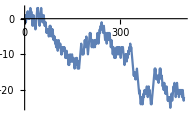

```mathematica
ListLinePlot[NestList[#+RandomChoice[{+1,-1}]&,0,500]]
```

So far, we’ve used NestList iteratively—effectively to perform a chain of applications of a particular function. But you can also use it for recursion, in which the very pattern of applications of the function is itself nested.

This does a chain of applications of the function f:

```mathematica
NestList[f[#]&,x,3]
```

{x,f[x],f[f[x]],f[f[f[x]]]}

The pattern of applications of f is more complicated here:

```mathematica
NestList[f[#,#]&,x,3]
```

{x,f[x,x],f[f[x,x],f[x,x]],f[f[f[x,x],f[x,x]],f[f[x,x],f[x,x]]]}

Adding frames makes it a little easier to see what’s going on:

```mathematica
NestList[Framed[f[#,#]]&,x,3]
```

{x,f[x,x],f[f[x,x],f[x,x]],f[f[f[x,x],f[x,x]],f[f[x,x],f[x,x]]]}

Putting everything in columns shows the nested pattern of function applications.

The nested boxes are recursively combined in twos at each level:

```mathematica
NestList[Framed[Column[{#,#}]]&,x,3]
```

{x,x
x,x
x
x
x,x
x
x
x
x
x
x
x}

This gives a sequence of recursively nested grids:

```mathematica
NestList[Framed[Grid[{{#,#},{#,#}}]]&,x,3]
```

{x,x | x
x | x,x | x
x | x | x | x
x | x
x | x
x | x | x | x
x | x,x | x
x | x | x | x
x | x
x | x
x | x | x | x
x | x | x | x
x | x | x | x
x | x
x | x
x | x | x | x
x | x
x | x
x | x | x | x
x | x
x | x
x | x | x | x
x | x | x | x
x | x | x | x
x | x
x | x
x | x | x | x
x | x}

This forms the beginning of a fractal structure:

```mathematica
NestList[Framed[Grid[{{0,#},{#,#}}]]&,x,3]
```

{x,0 | x
x | x,0 | 0 | x
x | x
0 | x
x | x | 0 | x
x | x,0 | 0 | 0 | x
x | x
0 | x
x | x | 0 | x
x | x
0 | 0 | x
x | x
0 | x
x | x | 0 | x
x | x | 0 | 0 | x
x | x
0 | x
x | x | 0 | x
x | x}

It’s easy to get some pretty ornate recursive structures:

```mathematica
NestList[Flatten[{#,Rotate[#,90°],Rotate[#,270°]}]&,"R",4]
```

{R,{R,R,R},{R,R,R,{R,R,R},{R,R,R}},{R,R,R,{R,R,R},{R,R,R},{R,R,R,{R,R,R},{R,R,R}},{R,R,R,{R,R,R},{R,R,R}}},{R,R,R,{R,R,R},{R,R,R},{R,R,R,{R,R,R},{R,R,R}},{R,R,R,{R,R,R},{R,R,R}},{R,R,R,{R,R,R},{R,R,R},{R,R,R,{R,R,R},{R,R,R}},{R,R,R,{R,R,R},{R,R,R}}},{R,R,R,{R,R,R},{R,R,R},{R,R,R,{R,R,R},{R,R,R}},{R,R,R,{R,R,R},{R,R,R}}}}}

Not all results from recursion are so complicated. Here’s an example that successively adds two shifted copies of a list together, as in {0,1,2,1}+{1,2,1,0}.

Prepend and append 0 to a list, then add together:

```mathematica
NestList[Join[{0},#]+Join[#,{0}]&,{1},5]
```

{{1},{1,1},{1,2,1},{1,3,3,1},{1,4,6,4,1},{1,5,10,10,5,1}}

If you put the result in a grid, it forms Pascal’s triangle of binomial coefficients:

```mathematica
NestList[Join[{0},#]+Join[#,{0}]&,{1},8]//Grid
```

1 |  |  |  |  |  |  |  | 
1 | 1 |  |  |  |  |  |  | 
1 | 2 | 1 |  |  |  |  |  | 
1 | 3 | 3 | 1 |  |  |  |  | 
1 | 4 | 6 | 4 | 1 |  |  |  | 
1 | 5 | 10 | 10 | 5 | 1 |  |  | 
1 | 6 | 15 | 20 | 15 | 6 | 1 |  | 
1 | 7 | 21 | 35 | 35 | 21 | 7 | 1 | 
1 | 8 | 28 | 56 | 70 | 56 | 28 | 8 | 1

NestList is set up to recursively generate a list by repeatedly applying a function that gives a single result. But what if one has a function that gives multiple results? A list is no longer sufficient to represent what happens; instead one has to use a graph. And that’s where NestGraph comes in.

If one actually only has one result at each step, NestGraph produces a simple chain of results:

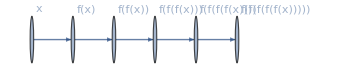

```mathematica
NestGraph[{f[#]}&, x, 5, VertexLabels->Automatic]
```

With two results at each step, however, it gives a tree:

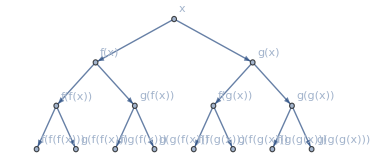

```mathematica
NestGraph[{f[#],g[#]}&, x, 3, VertexLabels->Automatic]
```

There are two edges that come out of each node here, one representing the result of applying f, the other representing the result of applying g.

With the functions 2# and 2#+1, you still get a tree:

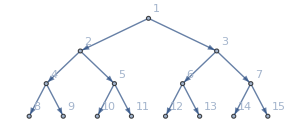

```mathematica
NestGraph[{2#,2#+1}&,1,3,VertexLabels->All]
```

But with 2# and #+1, you don’t:

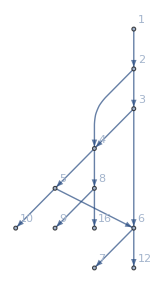

```mathematica
NestGraph[{2#,#+1}&,1,4,VertexLabels->All]
```

With {2#, 2#+1}&, it works out that you’re always generating different numbers. But with {2#,#+1}&, you sometimes end up generating the same number in different ways. For example, 2#& applied to 2 gives 4. #+1& applied to 2 gives 3. But applying #+1& to 3 again gives 4. So this means there are two ways to get to 4, as represented by two “branches” merging at 4 in the graph generated by NestGraph.

Let’s say our function takes any country and gives a list of countries that border it. Starting from Switzerland, here’s the graph we get after one step, in effect showing the immediate neighbors of Switzerland.

One step in generating a graph of bordering countries around Switzerland:

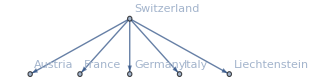

```mathematica
NestGraph[#["BorderingCountries"]&,LinguisticAssistant,1,VertexLabels->All]
```

Two steps, with lots of merging:

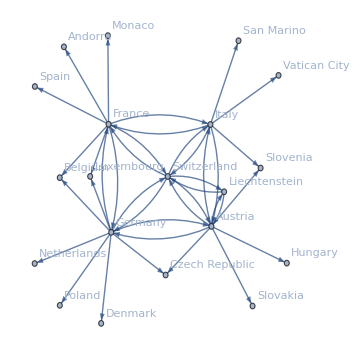

```mathematica
NestGraph[#["BorderingCountries"]&,LinguisticAssistant,2,VertexLabels->All]
```

The result of NestGraph is here showing us a network that includes not just immediate neighbors, but also neighbors of neighbors.

As another example, start from the word “hello” and successively connect every word to 3 words in the list of common words that Nearest considers nearest to it.

Create a network of nearby words with respect to 1-letter changes:

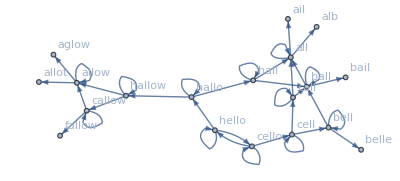

```mathematica
NestGraph[Nearest[WordList[ ],#,3]&,"hello",4,VertexLabels->All]
```

Within this graph, we can now find the shortest path from “hello” to “fallow”:

```mathematica
FindShortestPath[-Graphics-,"hello","fallow"]
```

{hello,hallo,hallow,callow,fallow}

Vocabulary

NestList[ f,x,n] |   | make a list of applying  f to x up to n times
Nest [f,x,n] |   | give the result of applying  f to x exactly n times 
NestGraph[ f,x,n] |   | make a graph by nestedly applying  f starting with x

"11 Exercises Available"
"with 5 extras" | "Get Started »"

Make a list of the results of nesting Blur up to 10 times, starting with a rasterized size-30 “X”. »

| Expected output: |  
  | {,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-} |

Start with x, then make a list by nestedly applying Framed up to 10 times, using a random background color each time. »

| Sample expected output: |  
  | {x,x,x,x,x,x,x,x,x,x,x} |

Start with a size-50 “A”, then make a list of nestedly applying a frame and a random rotation 5 times. »

| Sample expected output: |  
  | {"A","A","A","A","A","A"} |

Make a line plot of 100 iterations of the logistic map iteration 4 #(1-#)&, starting from 0.2. »

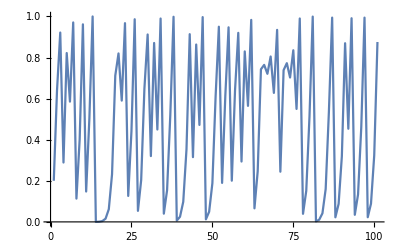
| Expected output: |  
  | -Graphics- |

Find the numerical value of the result from 30 iterations of 1+1/#& starting from 1. »

| Expected output: |  
  | 1.61803 |

Create a list of the first 10 powers of 3 (starting at 0) by nested multiplication. »

| Expected output: |  
  | {1,3,9,27,81,243,729,2187,6561,19683} |

Make a list of the result of nesting the (Newton’s method) function (#+2/#)/2& up to 5 times starting from 1.0, and then subtract √2from all the results. »

| Expected output: |  
  | {-0.414214,0.0857864,0.0024531,2.1239×10^-6,1.59472×10^-12,-2.22045×10^-16} |

Make graphics of a 1000-step 2D random walk which starts at {0,0}, and in which at each step a pair of random numbers between −1 and +1 are added to the coordinates. »

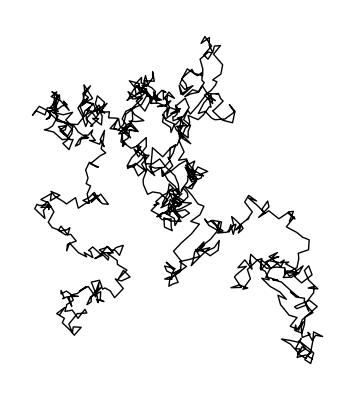
| Sample expected output: |  
  | -Graphics- |

Make an array plot of 50 steps of Pascal’s triangle modulo 2 by starting from {1} and nestedly joining {0} at the beginning and at the end, and adding these results together modulo 2. »

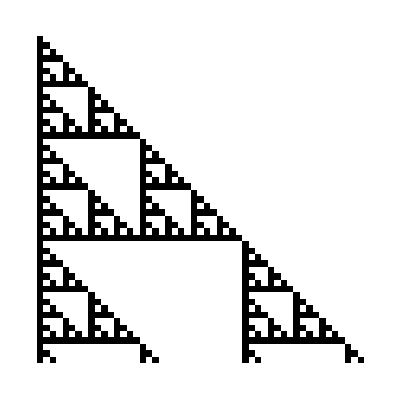
| Expected output: |  
  | -Graphics- |

Generate a graph by starting from 0, then nestedly 10 times connecting each node with value n to ones with values n+1 and 2n. »

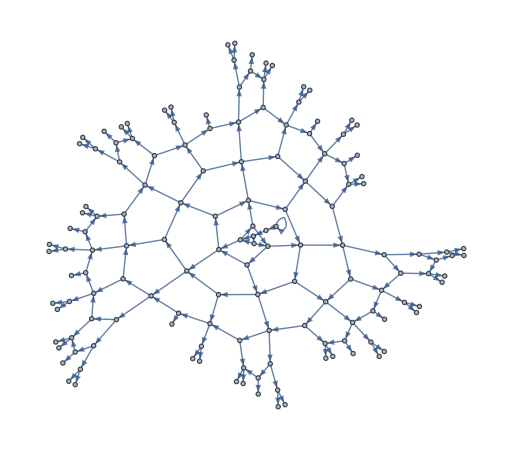
| Expected output: |  
  | -Graphics- |

Generate a graph obtained by nestedly finding bordering countries starting from the United States, and going 4 iterations. »

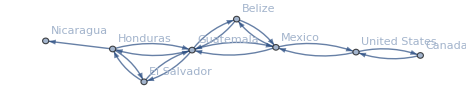
| Expected output: |  
  | -Graphics- |

Make a line plot of 100 iterations of linear congruential function Mod[59#,101]&, starting from 1. »

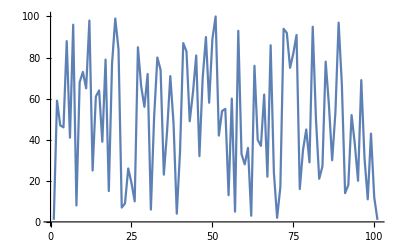
| Expected output: |  
  | -Graphics- |

Create a list of 5 power towers of 2, i.e. 2^2^2...^2 n times, with n from 0 to 4. »

| Expected output: |  
  | {1,2,4,16,65536} |

Create a list of 20 power towers of 1.2, i.e. 1.2^1.2^...^1.2 n times, with n from 0 to 19. »

| Expected output: |  
  | {1,1.2,1.24456,1.25472,1.25704,1.25758,1.2577,1.25773,1.25773,1.25773,1.25773,1.25773,1.25773,1.25773,1.25773,1.25773,1.25773,1.25773,1.25773,1.25773} |

Generate a list of the numerical values obtained by up to 10 nestings of the function Sqrt[1+#]&. »

| Expected output: |  
  | {1.,1.41421,1.55377,1.59805,1.61185,1.61612,1.61744,1.61785,1.61798,1.61802,1.61803} |

Make graphics of a 1000-step 3D random walk which starts at {0,0,0}, and in which at each step a triple of random numbers between −1 and +1 are added to the coordinates. »

| Expected output: |  
  | -Graphics3D- |

Q&A

What’s the difference between iteration and recursion?

If one does one thing repeatedly, it’s iteration. When one takes the result of an operation and applies the same operation to it wherever it is, that’s recursion. It’s slightly confusing, because simple cases of recursion are just iteration. NestList always does recursion, but if only one slot appears in the function, the recursion can be “unrolled” into iteration.

What is the relation between nesting, recursion and fractals?

They are very closely related. The definitions aren’t precise, but fractals are basically geometrical forms that exhibit some type of nested or recursive structure.

What is Pascal’s triangle?

It’s a very common structure discussed in elementary mathematics. Its definition is very close to the Wolfram Language code here: at each row each number is computed as the sum of the numbers directly above it and above it to its right. Each row gives the coefficients in the expansion of (1+x)^n.

Is NestGraph like a web crawler?

Conceptually yes. One can think of it as doing the analog of starting from a webpage and then visiting links from that page, and continuing recursively with that process. We’ll see an example of this in Section 44.

Why do some but not all countries have arrows both ways in the bordering countries graph?

If NestGraph was run for enough steps, all countries would have arrows both ways, since if A borders B, then B borders A. But here we’re stopping after just 2 steps, so many of the reverse connections haven’t been reached.

Why use NestList for something like NestList[2*#&,1,15]?

You don’t need to. You can just use Power, as in Table[2^n,{n,0,15}]. But it’s nice to see the sequence Plus, Times, Power arise from successive nesting (e.g. NestList[2+#&,0,15] is Table[2*n,{n,0,15}]).

Is there a way to keep applying a function until nothing is changing?

Yes. Use FixedPoint or FixedPointList (see Section 41).

Tech Notes

NestList effectively traces out a “single path of computation”. NestGraph can be thought of as tracing out multiple “entangled” paths, to yield a multiway graph.

NestGraph can be used, for example, to generate game graphs by having the results at each step correspond to possible moves in a game.

Many examples of “nondeterministic computation” can be thought of as finding paths in graphs generated by NestGraph. Examples include theorem proving and parsing.

The nearest words example can be made much more efficient by first computing a NearestFunction, then using this repeatedly, rather than computing Nearest from scratch for every word. This example is also closely related to NearestNeighborGraph, discussed in Section 22.

More to Explore

Guide to Functional Iteration in the Wolfram Language »